```mathematica
Remove["Global`*"];
ClearAll["Global`*"];
Get[NotebookDirectory[]<>"QBMMlib.wl"];
Get[NotebookDirectory[]<>"TimeSteppers.wl"];
```

```mathematica
model="nonlinear";
If[model=="linear",
	Ca=1/2;γ=1;Rey=Infinity;
	Cp0=1;
	Cp[t_]:=Cp0;
	Toneperiod=3.4 (1/Cp0)^0.75;
];
If[model=="nonlinear",
	Ca=1/2;γ=1;
	Cp0=0.9;
	(*Cp0=1/0.7;*)
	Toneperiod=3.4 2  (1/Cp0)^0.75;
	(*Cp[t_]:=Cp0;*)
	Cp[t_]:=If[t<Toneperiod,Cp0 Sin[2 Pi t/Toneperiod]+1,1];
];
Nperiod=0.5;
T=Nperiod Toneperiod;

dt=1.  10^-5;dt0=dt;
dtmin=dt;dtmax=1000dt;
tol=1 10^-5;

μR=1.;σR=0.1;
μRd=10^-14;σRd=0.1;
μRo=1.;σRo=0.1;
𝒟r=LogNormalDistribution[Log[μR],σR];
𝒟v=NormalDistribution[μRd,σRd];
RRdPDF=ProductDistribution[𝒟r,𝒟v];
(*RRdPDF=BinormalDistribution[{μR,μRd},{σR,σRd},0.1];*)
```

```mathematica
dimensions=3;
If[dimensions==2,
	nro=1;
	Ros={1};wRos={1};
];
If[dimensions==3,
	nro=5;
	𝒟ro=LogNormalDistribution[Log[μRo],σRo];
	RRdRoPDF=ProductDistribution[𝒟r,𝒟v,𝒟ro];
	momRo[i_]:=Moment[𝒟ro,i];
	momRos=Table[momRo[i],{i,0,2nro-1}];
	{Ros,wRos}=wheeler[momRos,nro];
	If[Min[Ros]<0,Print["Negative Ro!"];Abort[];];
	momRRd[i_,j_,k_:0]:=Moment[RRdPDF,{i,j}];
];

method="CHyQMOM";(*"CQMOM" or "CHyQMOM"*)
nr=2;
nrd=2;
numperm=2;
If[method=="CHyQMOM"&&nr==3,qmax=1];

ks=momidx[nr,nrd,method,numperm,nro];
ksp={{3,0,0},{2,1,0},{3,2,0},{3(1-γ),0,3γ}};
```

```mathematica
frhs[mom_,t_,l_,m_,n_]:=Module[{},
	If[model=="linear",Return[l mom[l-1,m+1,n]-m(mom[l,m,n]+ mom[l+1,m-1,n]-mom[l,m-1,n+1]+Cp[t] mom[l,m-1,n]),Module]];
	If[model=="nonlinear",
		If[dimensions==2,Return[l mom[l-1,m+1,0]+m(mom[l-1-3γ,m-1,0]-3/2 mom[l-1,m+1,0]-Cp[t] mom[l-1,m-1,0]),Module]];
		If[dimensions==3,Return[l mom[l-1,m+1,n]+m(mom[l-1-3γ,m-1,n+3γ]-3/2 mom[l-1,m+1,n]-Cp[t] mom[l-1,m-1,n]),Module]];
	];
];

myrhs[moms_,t_]:=Module[{mom,rhs,momout,rhs1,rhs2,momsp1,momsp2,momout1,momout2,w},
	If[method=="CHyQMOM",
		{w,xix,xiy}=chyqmom[moms,ks,qmax,wRos,Ros];
		{momout,momsp,mom}=quad[w,xix,xiy,method,nr,nrd,ks,ksp,0,nro,wRos,Ros];
		rhs=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
	];
	If[method=="CQMOM",
		If[numperm==2,
			{w,xi,xis}=cqmom12[moms,ks,nr,nrd,nro,wRos,Ros];
			{momout1,momsp1,mom}=quad[w,xi,xis,method,nr,nrd,ks,ksp,12,nro,wRos,Ros];
			rhs1=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
		
			{w,xi,xis}=cqmom21[moms,ks,nr,nrd,nro,wRos,Ros];
			{momout2,momsp2,mom}=quad[w,xi,xis,method,nr,nrd,ks,ksp,21,nro,wRos,Ros];
			rhs2=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];

			momsp=(momsp1+momsp2)/2;
			momout=(momout1+momout2)/2;
			rhs=(rhs1+rhs2)/2;
		,
			{w,xi,xis}=cqmom12[moms,ks,nr,nrd,nro,wRos,Ros];
			{momout,momsp,mom}=quad[w,xi,xis,method,nr,nrd,ks,ksp,12,nro,wRos,Ros];
			rhs=Table[frhs[mom,t,ks[[i,1]],ks[[i,2]],ks[[i,3]]],{i,Length[ks]}];
		];
	];
	Return[{momout,rhs},Module];
];
```

```mathematica
moms=Table[Sum[wRos[[l]] Ros[[l]]^ks[[i,3]] momRRd[ks[[i,1]],ks[[i,2]],l],{l,1,nro}],{i,1,Length[ks]}];
sol={};ts={};dets={};abscissa={};spsol={};t=0;dt=dt0;
Monitor[While[t≤T,
	{moms,mome,e}=RK23[moms,myrhs,t,dt];

	If[method=="CHyQMOM",AppendTo[abscissa,Table[Thread[{xix[j],xiy[j]}],{j,nro}]]];
	If[method=="CQMOM",AppendTo[abscissa,Table[Flatten[Table[Thread[{xis[j][i],xi[j][[i]]}],{i,nrd}],1],{j,nro}]]];
	AppendTo[sol,moms];AppendTo[spsol,momsp];
	AppendTo[ts,t];

	t=t+dt;
	dt=dt Min[Max[Sqrt[tol/(2 e)],0.3],2.];
dt=Min[Max[0.9 dt,dtmin],dtmax];

If[Norm[moms]>10^8,Print["Crash ",100 t/T];Break[]];
];
,TableForm[{{"Time",100t/T},{"δt",dt/dt0},{"Moments",Max[Abs[moms]]}}]
];
Length[ts]
```

391

```mathematica
myn=100;
plottingfac=1;
myts=Table[ts[[i]],{i,1,Length[abscissa],Floor[Length[abscissa]/myn]}];
Do[myabscissa[j]=Table[abscissa[[i,j]],{i,1,Length[abscissa],Floor[Length[abscissa]/N[myn]]}],{j,nro}];
Do[
	xdat[j]=myabscissa[j][[All,All,1]];
	ydat[j]=myabscissa[j][[All,All,2]];
	xmax[j]=If[Max[xdat[j]]>0,1.2 Max[xdat[j]],0.8 Max[xdat[j]]];
	xmin[j]=If[Min[xdat[j]]<0,1.2 Min[xdat[j]],0.8 Min[xdat[j]]];
	ymax[j]=If[Max[ydat[j]]>0,1.2 Max[ydat[j]],0.8 Max[xdat[j]]];
	ymin[j]=If[Min[ydat[j]]<0,1.2Min[ydat[j]],0.8 Min[ydat[j]]];
,{j,nro}];
xminF=Min[Table[xmin[j],{j,nro}]];
xmaxF=Max[Table[xmax[j],{j,nro}]];
yminF=Min[Table[ymin[j],{j,nro}]];
ymaxF=Max[Table[ymax[j],{j,nro}]];

dat3d=Table[Flatten[Table[Table[Flatten[{Ros[[j]],myabscissa[j][[k,i]]},1],{i,Length[myabscissa[j][[k]]]}],{j,nro}],1],{k,Length[myabscissa[1]]}];
```

```mathematica
ListAnimate[ParallelTable[
ListPlot[
	Table[myabscissa[j][[i]],{j,nro}],PlotRange->{{xminF,xmaxF},{yminF,ymaxF}},AxesLabel->{"R","V"}]
,{i,1,Length[myabscissa[1]]/plottingfac}]]
```

```mathematica
ListAnimate[
	ParallelTable[
		ListPointPlot3D[dat3d[[i]],PlotRange->{{0.9Min[Ros],1.1Max[Ros]},{xminF,xmaxF},{yminF,ymaxF}},
			AxesLabel->{"Ro","R","V"}]
	,{i,Length[dat3d]/plottingfac}],
	AnimationRunTime->0.1
]
```

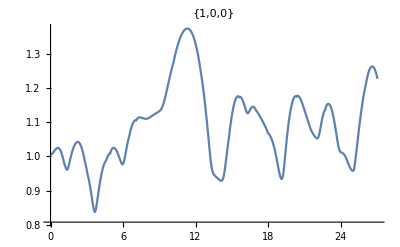
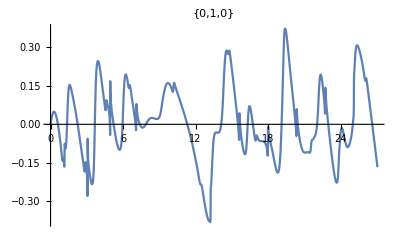
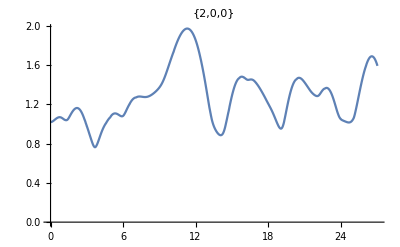
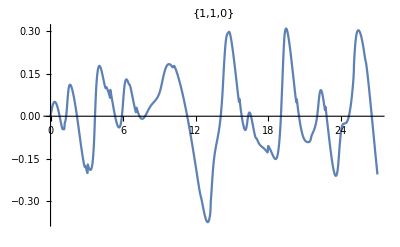
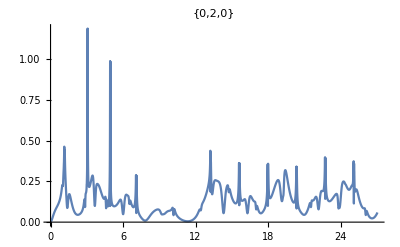
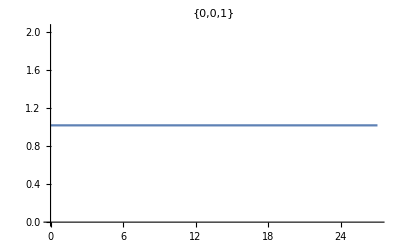
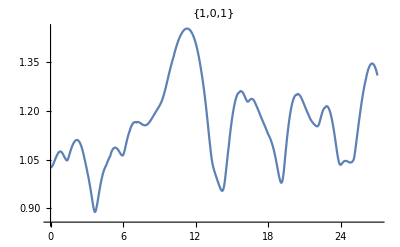
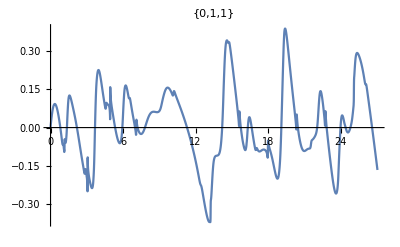

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[Thread[{ts,sol[[All,i]]}],Joined->True,PlotRange->All,PlotLabel->ks[[i]]]]
]
,{i,1,Length[moms]}]
plots
```

```mathematica
(* Verify with Monte Carlo *)
Ncases=3000;
cases=RandomVariate[RRdRoPDF,Ncases];

Clear[t];
If[model=="linear",
	β=2/Rey;ω2= 2 γ Ca;
	myr=ParallelTable[
	r[t]/.(NDSolve[
{r''[t] == -2 β r'[t]-ω2 r[t]-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
If[model=="nonlinear",
	myr=ParallelTable[
r[t]/.(NDSolve[
{r[t]r''[t]+3/2 r'[t]^2 ==(cases[[i,3]]/r[t])^(3 γ)-Cp[t],r[0]==cases[[i,1]],r'[0]==cases[[i,2]]},
r[t],
{t,0,T}]//First//First),
{i,Ncases}];
];
mydr=ParallelTable[D[myr[[i]],t],{i,Ncases}];

Nt=100;ts2=Table[i,{i,0,T,T/Nt}];
ts2=myts;Nt=Length[ts2];
P=Table[
	Table[
	{
	myr[[j]]/.{t->ts2[[i]]},
	mydr[[j]]/.{t->ts2[[i]]},
	cases[[j,3]]
	}
	,{j,Ncases}]
,{i,Nt}];

mcmoms=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ks[[j,1;;3]]]},{i,Nt}],{j,Length[ks]}];
mcmomssp=ParallelTable[Table[{ts2[[i]],Moment[P[[i]],ksp[[j,1;;3]]]},{i,Nt}],{j,Length[ksp]}];
```

```mathematica
plts=ParallelTable[
Show[
DensityHistogram[P[[i]],PlotRange->{{xmin,xmax},{ymin,ymax},All}],
ListPlot[myabscissa[[i]],PlotStyle->Red,PlotRange->{{xmin,xmax},{ymin,ymax}}]]
,{i,1,Length[P]/1}];
vid=ListAnimate[plts]
```

```mathematica
(*Export["~/Desktop/movie.avi",vid]*)
```

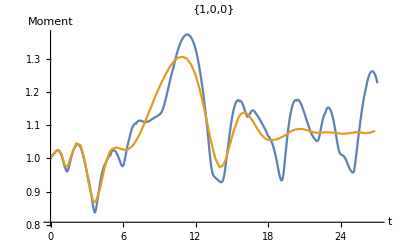
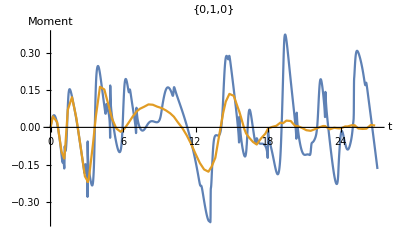
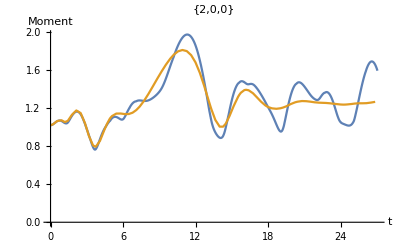
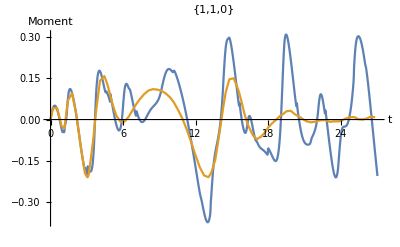
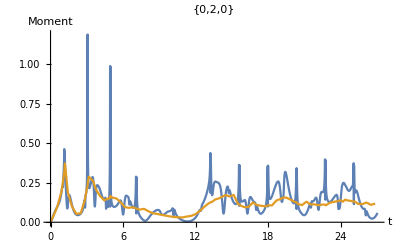
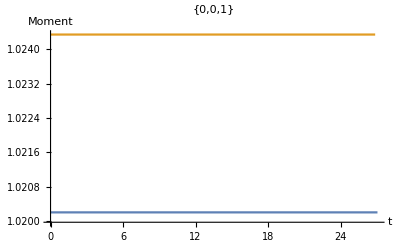
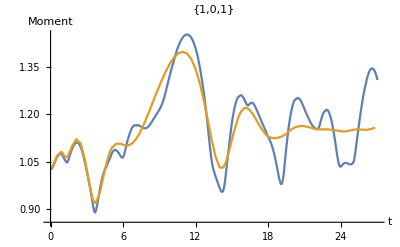
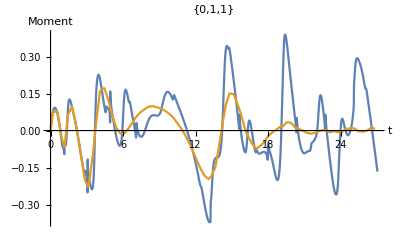

```mathematica
plots={};
Do[
If[Total[ks[[i]]]<10&&Total[ks[[i]]]>0,
AppendTo[plots,ListPlot[{Thread[{ts,sol[[All,i]]}],mcmoms[[i]]},Joined->True,PlotRange->All,PlotLabel->ks[[i]],AxesLabel->{"t","Moment"}]]
]
,{i,1,Length[moms]}]
plots

plots={};
Do[
AppendTo[plots,ListPlot[{Thread[{ts,spsol[[All,i]]}],mcmomssp[[i]]},Joined->True,PlotRange->All,PlotLabel->ksp[[i]],AxesLabel->{"t","Moment"}]]
,{i,1,Length[momsp]}]
plots
```

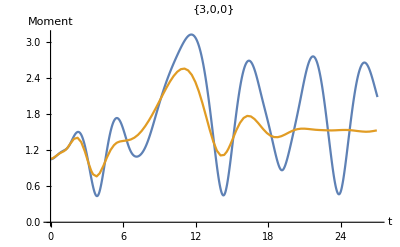
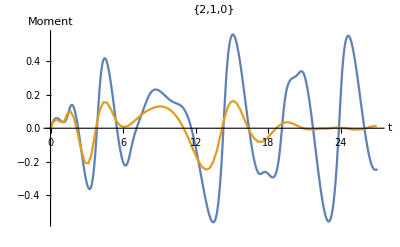
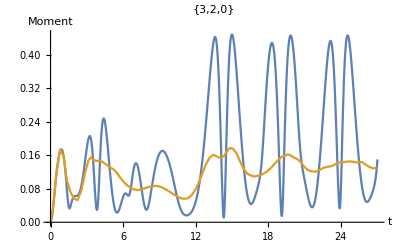
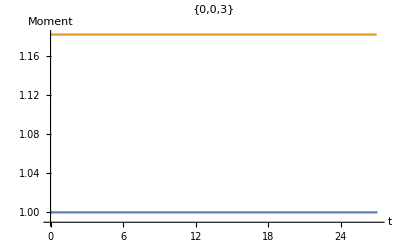

```mathematica
asdf
```